```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
tab=Import["testdata_mat.txt","Table"];
Evalues = tab[[5]];
qvalues = tab[[8]];
Kvalues=tab[[11;;]];
KEvalues[NE_]:=Transpose[{qvalues,Kvalues[[NE]]}]
```

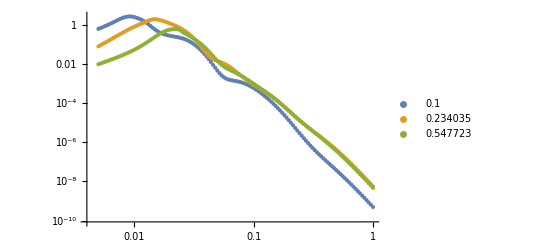

```mathematica
ListLogLogPlot[{KEvalues[1],KEvalues[2],KEvalues[3]},PlotLegends->{Evalues[[1]],Evalues[[2]],Evalues[[3]]}]
```

```mathematica
KE[NE_]:=Interpolation[Transpose[{qvalues,Kvalues[[NE]]}]];
```

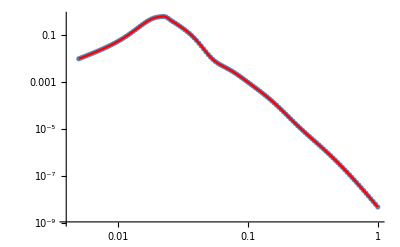

```mathematica
Eindex=3;
Show[ListLogLogPlot[KEvalues[Eindex]],LogLogPlot[KE[Eindex][q],{q,0.005,1},PlotStyle->Red]]
```

```mathematica
loglogdata=Flatten[Table[{{Log[Evalues[[i]]],Log[qvalues[[j]]]},Log[Kvalues[[i,j]]]},{i,1,Length[Evalues]},{j,1,Length[qvalues]}],1];
```

```mathematica
loglogKion = Interpolation[loglogdata]
```

InterpolatingFunction[…]

```mathematica
Kion[dE_,q_]:=Exp[loglogKion[Log[dE],Log[q]]]
```

0.390879

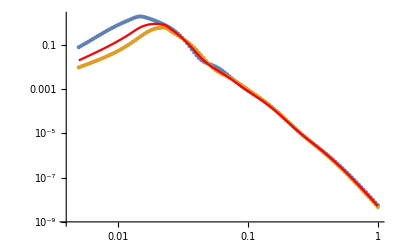

```mathematica
Eindex=2;
Emid=(0.5Evalues[[Eindex]]+0.5Evalues[[Eindex+1]])
Show[ListLogLogPlot[{KEvalues[Eindex],KEvalues[Eindex+1]}],LogLogPlot[Kion[Emid,q],{q,0.005,1},PlotStyle->Red]]
```